Boxcar

-HeavisideTheta[-1/2+θ/a]+HeavisideTheta[1/2+θ/a]

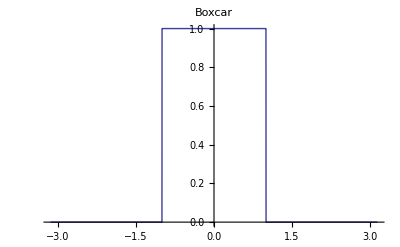

Autocorrelation of boxcar

(-2+ϕ) HeavisideTheta[-2+ϕ]-2 ϕ HeavisideTheta[ϕ]+(2+ϕ) HeavisideTheta[2+ϕ]

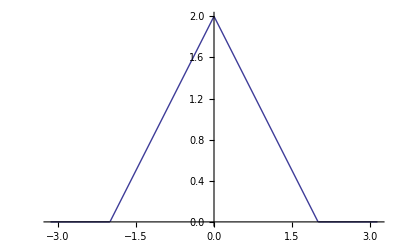

Autocorrelation of HeavisidePi

HeavisideLambda[x]

Fourier Transform of HeavisidePi Autocorrelation

Sinc[θ/2]^2/(√(2 π))

Fourier Transform of HeavisidePi

Sinc[θ/2]/(√(2 π))

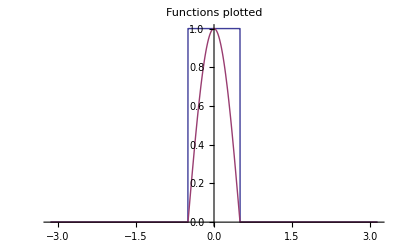

2 π (Sinc[π/2-ω/2]/(2 √(2 π))+Sinc[(π+ω)/2]/(2 √(2 π)))^2

Sinc[ω/2]^2/(√(2 π))

HeavisidePi[θ/2]

HeavisideLambda[θ]

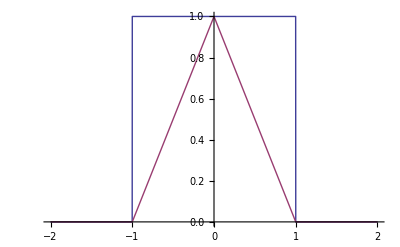

Sinc[y]

Sinc[y/2]^2

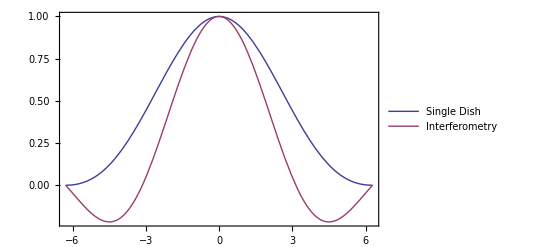

{4.07173×10^-20,{y→-2.78311}}

{1.15824×10^-22,{y→-1.89549}}

```mathematica
Remove["Global`*"]
HankelTransform[f_,a_,b_]:=2π Integrate[f a BesselJ[0,2π a b],{a,0,∞}]
Jinc[x_]:=(2 BesselJ[1,x])/x
Print["Boxcar"]
Boxcar[θ_,a_]=HeavisideTheta[θ/a+1/2]-HeavisideTheta[θ/a-1/2]
Plot[Boxcar[θ,2],{θ,-π,π},Exclusions->None,PlotLabel->"Boxcar"]
Print["Autocorrelation of boxcar"]
Convolve[Boxcar[θ,2],Boxcar[θ,2],θ,ϕ]
Plot[%,{ϕ,-π,π}]
Print["Autocorrelation of HeavisidePi"]
Convolve[HeavisidePi[y],HeavisidePi[y],y,x]
Print["Fourier Transform of HeavisidePi Autocorrelation"]
FourierTransform[%%,x,θ]
Print["Fourier Transform of HeavisidePi"]
FourierTransform[HeavisidePi[y],y,θ]
Plot[{HeavisidePi[θ],HeavisidePi[θ]Cos[π θ],%%},{θ,-π,π},Exclusions->None,PlotLabel->"Functions plotted"]
2π FourierTransform[HeavisidePi[θ]Cos[π θ],θ,ω]^2
(*2 Integrate[HeavisidePi[θ]Cos[π θ] HeavisidePi[θ-ϕ]Cos[π (θ-ϕ)],{θ,-1/2,1/2},Assumptions->{ϕ∈Reals}]*)
FourierTransform[Convolve[HeavisidePi[y],HeavisidePi[y],y,ϕ],ϕ,ω]
(*Plot[{%%,%},{ω,-4π,4π},PlotLegends->{HeavisidePi[θ]Cos[π θ],HeavisidePi[θ],},PlotRange->All]
FourierTransform[Boxcar[θ,1],θ,ω]^2
Convolve[Boxcar[θ,1],Boxcar[θ,1],θ,ϕ]
(1/√(2π))FourierTransform[%,ϕ,ω]
Plot[{%%%,%},{ω,-4π,4π}]
Print["FourierTransform for Circularly symmetric object becomes a Hankel transform"]*)
Interferometervis=HeavisidePi[ θ/2]
SingledishAutoCor=Convolve[HeavisidePi[ ϕ],HeavisidePi[ ϕ],ϕ,θ]
Plot[{Interferometervis,SingledishAutoCor},{θ,-2,2},Exclusions->None]
ibeam[y_]=FourierTransform[ Interferometervis,θ,y];
interbeam[y_]=ibeam[y]/ibeam[0]  
sbeam[y_]=FourierTransform[SingledishAutoCor,θ,y];
singlebeam[y_]=sbeam[y]/sbeam[0]
Plot[{singlebeam[y],interbeam[y]},{y,-2π,2π},PlotLegends->{"Single Dish","Interferometry"},Frame->True,FrameTicksStyle->White]
NMinimize[{(singlebeam[y]-1/2)^2,-4<y<0},y]
NMinimize[{(interbeam[y]-1/2)^2,-4<y<0},y]
```

```mathematica
Plot[{Jinc
```